# Spectrum for XXZ with two sites

## Hamiltonian

```mathematica
H =({{-Δ/4, 0, 0, 0}, {0, Δ/4, -1/2, 0}, {0, -1/2, Δ/4, 0}, {0, 0, 0, -Δ/4}});
```

## Spectrum

```mathematica
{evals, evecs}=Eigensystem[H]
```

{{1/4 (-2+Δ),-Δ/4,-Δ/4,(2+Δ)/4},{{0,1,1,0},{0,0,0,1},{1,0,0,0},{0,-1,1,0}}}

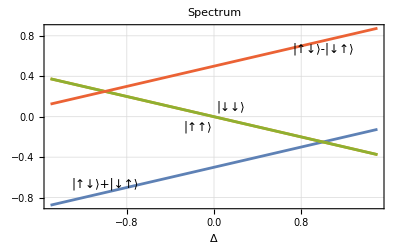

```mathematica
Plot[evals, {Δ, -3/2, 3/2}, PlotLabel->Text[Style["Spectrum", Black, Bold]], Epilog->{Text[Style["|↑↓⟩-|↓↑⟩",12],{1,2/3},{-1,0}],Text[Style["|↑↓⟩+|↓↑⟩", 12],{-1,-2/3},{0,-1}],Text[Style["|↑↑⟩", 12],{-0.15,-0.1},{0,0}],Text[Style["|↓↓⟩",12],{0.15,0.1},{0,0}]}, AxesLabel->{Text[Style["Δ", Black,12]],""}, Frame->True, GridLines->Automatic]
```